# MA2330

## 5.7 Summary

The solution of y'=A y associated with a real eigen value λ is 
	y(t)=ⅇ^(λ t)v 
where v is a matching eigenvector.

The solutions of y'=A y associated with a complex conjugate eigenvalue λ=a±b ⅈ are
	y_1(t) | = | ⅇ^at(cos(t) re(v)-sin(t) im(v))
y_2(t) | = | ⅇ^at(sin(t) re(v)+cos(t) im(v))
where v = re(v)±im(v) ⅈ are matching eigenvectors.

Eigenvalues of A give the long time behavior of the Dynamical System x'=A x

Complex a± b ⅈ are spirals in the re(v)—im(v) plane.

Spiral in for a<0 and out for a>0.

Spin fast for big b

Real λ<0 are attracting.

Real λ<0 are repelling.

```mathematica
Clear[ODEArrows]
ODEArrows[{λ_Real,v_}]:=If[λ>0, 
{Cyan,Thick,Arrow[{0*v, v}], Arrow[{0*v,-v}]},
{Green,Thick,Arrow[{v,0*v}], Arrow[{-v,0*v}]}
]
ODEArrows[{λ_Complex,v_}]:=Module[
{a,b, tMax},
{a,b}=ReIm[λ];
{If[a<0,Blue,Red],Table[
Arrow[
Table[E^(a t)(Cos[b t+θ] Re[v]- Sin[b t+θ] Im[v]),
{t, -Log[2]/Abs[a],Log[2]/Abs[a], 0.1*Log[2]/Abs[a]}
]],{θ,0, π,π/6}]}
]
```

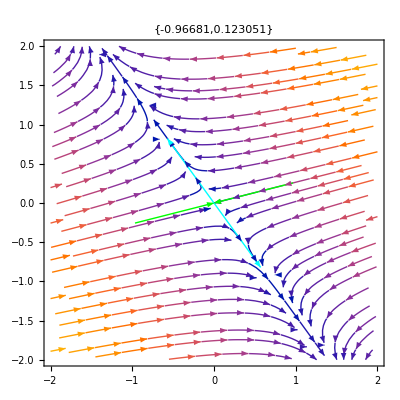

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];
{λ,V}=Chop[Eigensystem[A]];
StreamPlot[ A.{x1,x2},{x1,-2,2},{x2,-2,2},
PlotLabel->λ,
Epilog->Map[ODEArrows,{λ,V}ᵀ]]
```

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];
{λ,V}=Chop[Eigensystem[A]];
Show[
StreamPlot3D[A.{x1,x2,x3},{x1,-2,2},{x2,-2,2},{x3,-2,2},
StreamMarkers->"Arrow",
StreamStyle->Opacity[0.5]],
Graphics3D[Map[ODEArrows,{λ,V}ᵀ]],
PlotLabel->λ]
```

-Graphics3D-

## 5.8 Power Method x_(k+1)=A x_k

Computers order eigenvalues |λ_1|≥|λ_2|≥…≥|λ_n|. And normalize the eigenvectors ||v_i||=1.

If |λ_1| >|λ_2|then there is a simple way to compute the eigen vector associated with λ_1.  All you have to do is pick a random vector 
	x_0=c_1 v_1+c_(2 v_2)…+c_n v_n=∑_(j=1)^n c_i v_i
then the iterates x_k=A x_(k-1) converge to a multiple of v_1
	x_k=c_1 λ_1^k v_1+c_2 λ_2^k v_2+…+c_n λ_n^k v_n=∑_(j=1)^n c_i λ_i^k v_i
scale everything by λ_1^k to get
	x_k λ_1^-k=c_1 v_1+(c_2(λ_2/λ_1))^k v_2+…+(c_2(λ_n/λ_1))^k v_n→ c_1 v_1
In practice, any scaling works.  You do not need to know the eigenvalue.  This is called the power method.

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
x=RandomReal[{-1,1},m];
maxIter=33;
Data=Table[x=Normalize[A.x],{maxIter}];
TableForm[Data,TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4 | 5 | 6
1 | -0.820422 | -0.503507 | -0.199606 | 0.0171682 | 0.153953 | -0.0977218
2 | -0.226672 | 0.283043 | 0.566104 | 0.638972 | -0.345487 | -0.142782
3 | -0.0369024 | -0.893978 | 0.315008 | -0.215127 | 0.040165 | 0.228732
4 | -0.648315 | 0.000315865 | 0.405985 | 0.22569 | -0.488396 | -0.354115
5 | -0.210803 | -0.663891 | 0.424483 | 0.382735 | -0.0627385 | 0.429188
6 | -0.359007 | -0.579622 | 0.567657 | -0.180886 | -0.297931 | -0.302381
7 | -0.397326 | -0.554395 | 0.394908 | 0.45334 | -0.183566 | 0.373648
8 | -0.349642 | -0.63567 | 0.615522 | -0.013304 | -0.268143 | -0.150761
9 | -0.404822 | -0.649327 | 0.472578 | 0.294703 | -0.21565 | 0.240435
10 | -0.398553 | -0.630166 | 0.594886 | 0.111246 | -0.275619 | -0.0426176
11 | -0.392939 | -0.666394 | 0.516756 | 0.235972 | -0.225586 | 0.167063
12 | -0.405189 | -0.642545 | 0.57546 | 0.141448 | -0.26779 | 0.00914773
13 | -0.397951 | -0.659578 | 0.533266 | 0.220793 | -0.236711 | 0.132052
14 | -0.401975 | -0.650967 | 0.566875 | 0.156491 | -0.259611 | 0.0377255
15 | -0.400984 | -0.657149 | 0.541369 | 0.207266 | -0.243304 | 0.110136
16 | -0.40154 | -0.653083 | 0.561457 | 0.169185 | -0.255561 | 0.0554902
17 | -0.401239 | -0.656786 | 0.546436 | 0.197477 | -0.246374 | 0.0966939
18 | -0.401787 | -0.653892 | 0.557878 | 0.176603 | -0.253484 | 0.0657443
19 | -0.401285 | -0.656294 | 0.549368 | 0.192263 | -0.248069 | 0.0891114
20 | -0.401747 | -0.654525 | 0.555811 | 0.180429 | -0.252208 | 0.0714548
21 | -0.401423 | -0.655865 | 0.550969 | 0.189452 | -0.24909 | 0.0848386
22 | -0.401659 | -0.654895 | 0.554651 | 0.182591 | -0.251445 | 0.0747052
23 | -0.4015 | -0.655628 | 0.551867 | 0.1878 | -0.249674 | 0.0823787
24 | -0.401619 | -0.65508 | 0.55398 | 0.183864 | -0.251013 | 0.0765768
25 | -0.401531 | -0.655501 | 0.552384 | 0.186836 | -0.250001 | 0.0809639
26 | -0.401601 | -0.655182 | 0.553592 | 0.184593 | -0.250768 | 0.077648
27 | -0.401547 | -0.655425 | 0.55268 | 0.186289 | -0.250188 | 0.0801555
28 | -0.401588 | -0.655242 | 0.55337 | 0.185006 | -0.250627 | 0.0782593
29 | -0.401558 | -0.655381 | 0.552849 | 0.185977 | -0.250295 | 0.0796937
30 | -0.401581 | -0.655276 | 0.553243 | 0.185243 | -0.250546 | 0.0786087
31 | -0.401563 | -0.655355 | 0.552945 | 0.185798 | -0.250356 | 0.0794294
32 | -0.401577 | -0.655296 | 0.553171 | 0.185378 | -0.2505 | 0.0788087
33 | -0.401567 | -0.655341 | 0.553 | 0.185696 | -0.250391 | 0.0792781

```mathematica
Eigenvectors[A,1]
```

{{-0.401571+0. ⅈ,-0.655321+0. ⅈ,0.553074+0. ⅈ,0.185559+0. ⅈ,-0.250438+0. ⅈ,0.079076+0. ⅈ}}

### Inverse Power Method x_(k+1)=(A-α I)^-1 x_k

The inverse power method 
	x_(k+1)=(A-α I)^-1 x_k
converges to an eigenvector with an eigenvalue near α.

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
x=RandomReal[{-1,1},m];
α=1.2;
maxIter=50;
Data=Table[x=Normalize[LinearSolve[A-α IdentityMatrix[m],x]],{maxIter}];
TableForm[Data,TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4 | 5 | 6
1 | 0.291037 | 0.464994 | -0.254528 | -0.756135 | 0.213604 | 0.130105
2 | 0.231122 | 0.820903 | 0.420465 | -0.19131 | 0.215757 | 0.112954
3 | 0.254971 | 0.82563 | 0.410657 | -0.190539 | 0.196552 | 0.0987253
4 | 0.253268 | 0.825692 | 0.410111 | -0.191707 | 0.198389 | 0.0989266
5 | 0.25338 | 0.825662 | 0.410162 | -0.191681 | 0.198264 | 0.0989812
6 | 0.25337 | 0.825665 | 0.410161 | -0.191679 | 0.198275 | 0.0989764
7 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
8 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
9 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
10 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
11 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
12 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
13 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
14 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
15 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
16 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
17 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
18 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
19 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
20 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
21 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
22 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
23 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
24 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
25 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
26 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
27 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
28 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
29 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
30 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
31 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
32 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
33 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
34 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
35 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
36 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
37 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
38 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
39 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
40 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
41 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
42 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
43 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
44 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
45 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
46 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
47 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
48 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
49 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767
50 | 0.253371 | 0.825664 | 0.410161 | -0.191679 | 0.198274 | 0.0989767

### Summary Power Method

The power method 
	y_(k+1) | = | A x_k
x_(k+1) | = | (y_(k+1))/(||y_(k+1)||)
converges to the eigenvector with the  "largest" eigenvalue.

The inverse power method 
	y_(k+1) | = | (A-α Id)^-1 x_k
x_(k+1) | = | (y_(k+1))/(||y_(k+1)||)
 converges to the eigenvector with the  eigenvalue "nearest" the shift α.

## 5.9 Markov Chains

A vector x with nonnegative entries that sum to one is a probability vector.

A square matrix P with non-negative entries and columns that sum to one is a  stochastic matrix

The Discrete Dynamical System x_k=P x_(k-1) with a stochastic matrix P and a probability vector x_0 as initial state is a Markov Chain.

The car matrix from exam 1 
	P=(0.9 | 0.1 | 0.3 | 0.2
0.1 | 0.8 | 0 | 0
0 | 0.1 | 0.7 | 0
0 | 0 | 0 | 0.8)	
is a stochastic matrix.  If we normalize the initial car vector by 428 (the total number of cars) we get
	x_0=(100
85
120
123)/428=(0.233645
0.198598
0.280374
0.287383)
This is a Markov chain.  It is not an accident that P has an eigen value of 1.

Theorem 10 : If P is a stochastic matrix then 1 is an eigenvalue of P.

Why?  P and Pᵀ have the same eigenvalues and since Pᵀ has row sums equal to one the vector of all ones is an eigenvector.

```mathematica
P=({{0.9, 0.1, 0.3, 0.2}, {0.1, 0.8, 0, 0}, {0, 0.1, 0.7, 0}, {0, 0, 0, 0.8}});
Pᵀ.{1,1,1,1}
```

{1.,1.,1.,1.}

A steady state vector satisfies P v =v.

A steady state vector is an eigenvector associated with the eigenvalue 1.

Theorem 11
Regular Markov chains x_k=P x_(k-1) converge to a unique steady state vector as k→∞.

A Markov Chain is  Regular if some matrix power P^k has strictly positive entries.

Regular means is that all the states are linked.